```mathematica
(*LaTeX Equation images*)
<<MaTeX`
tex[x_] := Pane[
	MaTeX[x, Magnification->2],
	Full, Alignment->Center]

print[x_] := CellPrint[ExpressionCell[
	Style[TraditionalForm[x], FontSize->20, FontFamily->"TR"], 
	"DisplayFormulaNumbered"]]

(*Set up plot theme*)
Themes`AddThemeRules["abestheme",
	DefaultPlotStyle->Thread@Directive[
		Darker[#]&/@{Blue,Red,Green,Magenta,Cyan,Orange},Thick],
		LabelStyle->Directive[Black, 13, 
			FontFamily-> "Times New Roman"],
	Frame->True, 
	FrameStyle->Directive[Black, 13, FontFamily->"Times New Roman"]];
```

# Representational Rényi Heterogeneity

## Closed-Form Analysis of Central vs. Tail-Mode Pruning in Gaussian Representational Rényi Heterogeneity

## Abraham Nunes, Martin Alda, Timothy Bardouille, and Thomas Trappenberg Dalhousie University, Halifax, Nova Scotia, Canada

The pooled covariance matrix in a mixture of Gaussians is computed as

```mathematica
poolcov = Subscript[Σ̃, j,k] == (1/n∑_(i=1)^n Subscript[Σ, i,j,k])+(1/n∑_(i=1)^n Subscript[μ, i,j] Subscript[μ, i,k])-1/n^2(∑_(i=1)^n Subscript[μ, i,j])(∑_(i=1)^n Subscript[μ, i,k])
```

(Σ̃)_(j,k)==-((∑_(i=1)^n μ_(i,j)) ∑_(i=1)^n μ_(i,k))/n^2+(∑_(i=1)^n μ_(i,j) μ_(i,k))/n+(∑_(i=1)^n Σ_(i,j,k))/n

```mathematica
ξ[n_][i_] := Extract[Normal[LeviCivitaTensor[n]], i];
```

```mathematica
σ[n_] := Permutations[Range[n],{n}];
```

The determinant is computed as follows:

```mathematica
n = 2;
∑_(k=1)^Length[σ[n]] ξ[2][σ[n][[k]]](∏_(i=1)^n Subscript[a, i,σ[n][[k,i]]])
```

-a_(1,2) a_(2,1)+a_(1,1) a_(2,2)

We initialize a series of normal distributions:

```mathematica
compdist[n_]:= Table[MultinormalDistribution[{i μ}, {{Subscript[σ, i]^2}}],{i,n}]
mixdist[dists_] := MixtureDistribution[
	Table[1/(Length@dists), Length@dists], dists]
```

and a pruning function:

```mathematica
GetMedianIdx[n_]:= {Floor[Median[Range[n]]], Select[Range[n], #≠Floor[Median[Range[n]]]&]}
PruneFromTail[dists_]:= dists[[1;;Length@dists-1]]
PruneFromCenter := Function[{dists}, 
	Module[{n,idx, mdn},
		n = Length@dists;
		idx = Range[n];
		mdn = Floor[Median[idx]];
		idx = Select[idx, #≠mdn&];
		dists[[idx]]
	]
]
```

The beta heterogeneity for a Gaussian mixture (at q=1) is:

```mathematica
gammahet[dists_]:= Sqrt[Det[Covariance[mixdist[dists]]]]
alphahet[dists_]:= Product[(Det[Covariance[dists[[i]]]])^(1/(2 Length@dists)), {i, Length@dists}]
betahet[dists_]:=gammahet[dists]/alphahet[dists]
```

```mathematica
betahetq[q_][dists_]:=Sqrt[Det[Covariance[mixdist[dists]]]] (Sum[(Det[Covariance[dists[[i]]]])^((1-q)/2), {i, Length@dists}]/(Length@dists))^(1/(q-1))
```

The difference between β-heterogeneity values for tail vs central pruning is as follows:

```mathematica
dbeta := Function[{n, prune},
Module[{diff, mdn, idx, rules},
diff = Piecewise[{{betahet[PruneFromTail[compdist[n]]]-betahet[compdist[n]], prune =="tail"}, {betahet[PruneFromCenter[compdist[n]]]-betahet[compdist[n]], prune == "center"}}];
{mdn, idx} = GetMedianIdx[n];
rules = Piecewise[{{Flatten[Catenate[{{Subscript[σ, n]->s}, Table[Subscript[σ, i]->1, {i, n-1}]}]], prune =="tail"}, {Flatten[Catenate[{{Subscript[σ, mdn]->s}, Table[Subscript[σ, i]->1, {i, idx}]}]], prune =="center"}}];
ReplaceAll[rules][diff]
]]
```

```mathematica
distributions := Function[{n, prune}, 
Module[{dists, mdn, idx, rules, rep},
{mdn, idx} = GetMedianIdx[n];
rules = Piecewise[{{Flatten[Catenate[{{Subscript[σ, n]->s}, Table[Subscript[σ, i]->1, {i, n-1}]}]], prune =="tail"}, {Flatten[Catenate[{{Subscript[σ, mdn]->s}, Table[Subscript[σ, i]->1, {i, idx}]}]], prune =="center"}}];
rep = Replace[rules];
Table[MultinormalDistribution[{i μ}, {{rep[Subscript[σ, i]]^2}}],{i,n}]
]]
```

```mathematica
Manipulate[Grid[{{
Show[Plot[{(ⅇ^(-1/2 (x-μ)^2))/(√(2 π)),(ⅇ^(-1/2 (x-2 μ)^2))/(√(2 π))}/.μ->m, {x, -5, 10}, PlotRange->Full, PlotStyle->Darker@Blue],
Plot[{(ⅇ^(-(x-3 μ)^2/(2 σ^2)))/(√(2 π) √(σ^2))}/.μ->m, {x, -5, 10}, PlotRange->Full, PlotStyle->Darker@Green],
Plot[((ⅇ^(-1/2 (x-2 μ)^2))/(3 √(2 π))+(ⅇ^(-1/2 (x-μ)^2))/(3 √(2 π))+(ⅇ^(-(x-3 μ)^2/(2 σ^2)))/(3 √(2 π) √(σ^2)))/.μ->m, {x, -5, 10}, PlotRange->Full, PlotStyle->Red],
Plot[((ⅇ^(-(x-μ)^2/2))/(2 √(2 π))+(ⅇ^(-(x-2 μ)^2/2))/(2 √(2 π)))/.μ->m, {x, -5, 10}, PlotRange->Full, PlotStyle->{Red, Dashed}],
Graphics[Text["Tail "<>ToString[N[dbeta[3, "tail"]/.{s->σ, μ->m}]], {7, 0.3}]],
Frame->True, FrameStyle->Directive[Black, 14], ImageSize->350], 
Show[Plot[{(ⅇ^(-1/2 (x-μ)^2))/(√(2 π)),(ⅇ^(-1/2 (x-3 μ)^2))/(√(2 π))}/.μ->m, {x, -5, 10}, PlotRange->Full, PlotStyle->{Darker@Blue}],
Plot[(ⅇ^(-(x-2 μ)^2/(2 σ^2)))/(√(2 π) √(σ^2))/.μ->m, {x, -5, 10}, PlotRange->Full, PlotStyle->{Darker@Green}],
Plot[((ⅇ^(-1/2 (x-3 μ)^2))/(3 √(2 π))+(ⅇ^(-1/2 (x-μ)^2))/(3 √(2 π))+(ⅇ^(-(x-2 μ)^2/(2 σ^2)))/(3 √(2 π) √(σ^2)))/.μ->m, {x, -5, 10}, PlotRange->Full, PlotStyle->{Red}],
Plot[((ⅇ^(-(x-μ)^2/2))/(2 √(2 π))+(ⅇ^(-(x-3 μ)^2/2))/(2 √(2 π)))/.μ->m, {x, -5, 10}, PlotRange->Full, PlotStyle->{Red, Dashed}],
Graphics[Text["Center "<>ToString[N[dbeta[3, "center"]/.{s->σ, μ->m}]], {7, 0.3}]],
Frame->True, FrameStyle->Directive[Black, 14], ImageSize->350]}}], {{σ, 1}, 0, 10}, {{m, 1}, 0, 2}]
```

## Analytical Demonstration of the Effects of Pruning

### q=1

We first compute the beta heterogeneities for the different distributions:

```mathematica
totalbetatail = FullSimplify@PowerExpand[betahet[compdist[3]]/. {Subscript[σ, 1]->1, Subscript[σ, 2]->1, Subscript[σ, 3]->s}]
tailbeta = FullSimplify@PowerExpand[betahet[PruneFromTail@compdist[3]]/. {Subscript[σ, 1]->1, Subscript[σ, 2]->1, Subscript[σ, 3]->s}]
totalbetacenter = FullSimplify@PowerExpand[betahet[compdist[3]]/. {Subscript[σ, 1]->1, Subscript[σ, 2]->s, Subscript[σ, 3]->1}]
centerbeta = FullSimplify@PowerExpand[betahet[PruneFromCenter@compdist[3]]/. {Subscript[σ, 1]->1, Subscript[σ, 2]->s, Subscript[σ, 3]->1}]
```

(√(2+s^2+2 μ^2))/(√3 s^(1/3))

(√(4+μ^2))/2

(√(2+s^2+2 μ^2))/(√3 s^(1/3))

√(1+μ^2)

#### Tail mode pruning

The change in beta-heterogeneity with tail pruning is

```mathematica
Δtail = totalbetatail - tailbeta
```

-1/2 √(4+μ^2)+(√(2+s^2+2 μ^2))/(√3 s^(1/3))

```mathematica
dtailsurf = Plot3D[Δtail, {s, 0, 5}, {μ, -5, 5}, 
PlotStyle->Cyan,
AxesStyle->Directive[Black, 13],
AxesLabel->Automatic, 
BaseStyle->{FontFamily->"Times New Roman"}]
Export["~/Desktop/dtailsurf.png", 
		dtailsurf,
		ImageResolution->500, 
		"AllowRasterization"->True];
```

-Graphics3D-

For which we can find the minimum (by symmetry we constrain μ≥0):

```mathematica
sol = FullSimplify@PowerExpand@N@Solve[Flatten[{#==0 & /@∇_{s,μ} Δtail, μ≥0}], {s, μ}, Reals]
```

{{s→1.,μ→0.},{s→3.36946,μ→3.21765}}

We can show that only {s=1,μ=0} is the global minimum by demonstrating that only at that point is the Hessian positive definite:

```mathematica
Eigenvalues[∇_{s,μ} (∇_{s,μ} Δtail)] /. # &/@sol
```

{{0.416667,0.444444},{-0.0401367,0.143083}}

Finally, we evaluate Δ(Tail) at {s=1,μ=0}

```mathematica
Δtail /. sol[[1]]
```

0.

which shows that the minimal change in between-osbervation heterogeneity that can occur with tail-mode pruning is 0, and this only occurs when all mixture components are identical.

#### Center mode pruning

```mathematica
Δcenter = totalbetacenter - centerbeta
```

-√(1+μ^2)+(√(2+s^2+2 μ^2))/(√3 s^(1/3))

```mathematica
dcentersurf = Plot3D[Δcenter, {s, 0, 5}, {μ, -5, 5}, 
PlotStyle->Yellow,
AxesStyle->Directive[Black, 13],
AxesLabel->Automatic, 
BaseStyle->{FontFamily->"Times New Roman"}]
Export["~/Desktop/dcentersurf.png", 
		dcentersurf,
		ImageResolution->500, 
		"AllowRasterization"->True];
```

-Graphics3D-

```mathematica
pruninggrid = Grid[{Style[#, FontFamily->"Times New Roman", FontSize->15]&/@{"Δ(Tail)", "Δ(Center)"}, {dtailsurf, dcentersurf}}]
Export["~/Desktop/pruninggrid.pdf", 
		pruninggrid,
		ImageSize->300, 
		ImageResolution->600,
		AspectRatio->1/2,
		"AllowRasterization"->True];
```

Δ(Tail) | Δ(Center)
-Graphics3D- | -Graphics3D-

Under central mode pruning, there is a local minimum, but it is a saddle point.

```mathematica
sol = Solve[Flatten[{#==0 & /@∇_{s,μ} Δcenter}], {s, μ}, Reals]
```

{{s→1,μ→0}}

```mathematica
Eigenvalues[∇_{s,μ} (∇_{s,μ} Δcenter)/. sol[[1]]]
```

{4/9,-1/3}

At {s=1, μ=0}, we have

```mathematica
Δcenter/.sol[[1]]
```

0

which again simply means that if the central mode distribution is identical to the other components, removing it will not change the beta-heterogeneity.

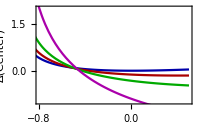

```mathematica
mus = {0, 1,2, 5};
colors = Darker@{Blue, Red, Green, Magenta};
epsfig = Legended[Show[Table[
Plot[Δcenter /. {s->1+ϵ, μ->mus[[i]]},{ϵ,-0.99,0.5}, PlotStyle->colors[[i]]], 
{i, Length@mus}], PlotRange->{{-0.8, 0.5}, {-1, 2}}, Frame->True, 
FrameStyle->Directive[Black,12], 
FrameLabel->{"σ_c-σ", "Δ(Center)"}, 
BaseStyle->{FontFamily->"Times New Roman"}, 
ImageSize->200], 
LineLegend[colors, Table[Style["μ="<>ToString[m], 
FontFamily->"Times New Roman"], {m,mus}]]]
```

```mathematica
expr = ApplySides[(#+√(1+μ^2))^2&, Δcenter  == 0]
```

```mathematica
FullSimplify[(2+s^2+2 μ^2)/(3 s^(2/3))==1+μ^2]
```

(2+s^2+2 μ^2)/(3 s^(2/3))==1+μ^2

```mathematica
FullSimplify@PowerExpand@Solve[(2+s^2+2 μ^2)/(3 s^(2/3))==1+μ^2,μ]
```

{{μ→-(√(3-(2+s^2)/s^(2/3)))/(√(-3+2/s^(2/3)))},{μ→(√(3-(2+s^2)/s^(2/3)))/(√(-3+2/s^(2/3)))}}

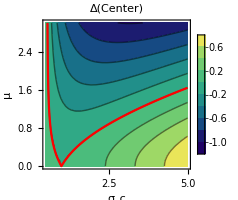

```mathematica
centerpruningfig = Show[Legended[Show[ContourPlot[Δcenter, {s, 0.5, 5},{μ, 0, 3}, 
ColorFunction->"BlueGreenYellow",
PlotLegends->Automatic,
PlotLabel->Style["Δ(Center)", Black, 13, FontFamily->"Times New Roman"],
ImageSize->200
], Plot[{(√(3-(2+s^2)/s^(2/3)))/(√(-3+2/s^(2/3)))}, {s, 0.5, 5}, 
PlotStyle->Red,
PlotRange->{{0.4, 5}, {0, 3}}], 
ImageSize->200, 
BaseStyle->{
FontFamily->"Times New Roman"},
FrameStyle->Directive[Black, 12],
FrameLabel->{"σ_c", "μ"}], 
Placed[Framed[
LineLegend[{Red}, 
		{Style["Δ(Center)|_σ_c=0", 
			FontFamily->"Times New Roman", 12]}],
Background->Opacity[0.8, White]], {0.5, 0.8}]
]]
Export["~/Desktop/centerpruningfig.pdf", 
		centerpruningfig,
		"AllowRasterization"->True];
```

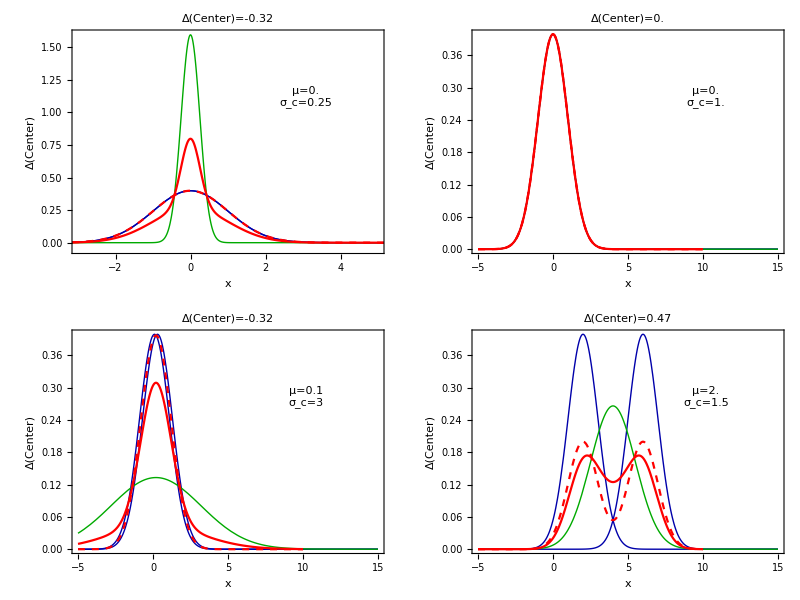
-Graphics- |

```mathematica
params = {{0., 0.25}, {0., 1.},{0.1, 3}, {2., 1.5}};
centerprunecases = Grid[ArrayReshape[Table[Show[Plot[{(ⅇ^(-1/2 (x-μ)^2))/(√(2 π)),(ⅇ^(-1/2 (x-3 μ)^2))/(√(2 π))}/.μ->p[[1]], {x, -5, 15}, PlotRange->{Piecewise[{{{-3, 5}, p[[2]]<0.5}, {Full, True}}], Piecewise[{{{-0.05,1.6}, p[[2]]<0.5}, {Full, True}}]}, PlotStyle->{Darker@Blue}, PlotTheme->"abestheme"],
Plot[(ⅇ^(-(x-2 μ)^2/(2 σ^2)))/(√(2 π) √(σ^2))/.{μ->p[[1]], σ->p[[2]]}, {x, -5, 15}, PlotRange->{Piecewise[{{{-3, 5}, p[[2]]<0.5}, {Full, True}}], Piecewise[{{{-0.05, 1.6}, p[[2]]<0.5}, {Full, True}}]}, PlotStyle->{Darker@Green}, PlotTheme->"abestheme"],
Plot[((ⅇ^(-1/2 (x-3 μ)^2))/(3 √(2 π))+(ⅇ^(-1/2 (x-μ)^2))/(3 √(2 π))+(ⅇ^(-(x-2 μ)^2/(2 σ^2)))/(3 √(2 π) √(σ^2)))/.{μ->p[[1]], σ->p[[2]]}, {x, -5, 10}, PlotRange->{Piecewise[{{{-3, 5}, p[[2]]<0.5}, {Full, True}}], Piecewise[{{{-0.05, 1.6}, p[[2]]<0.5}, {Full, True}}]}, PlotStyle->{Red}],
Plot[((ⅇ^(-(x-μ)^2/2))/(2 √(2 π))+(ⅇ^(-(x-3 μ)^2/2))/(2 √(2 π)))/.{μ->p[[1]], σ->p[[2]]}, {x, -5, 10}, PlotRange->{Piecewise[{{{-3, 3}, p[[2]]<1}, {Full, True}}], Piecewise[{{{-0.05, 1.6}, p[[2]]<0.5}, {Full, True}}]}, PlotStyle->{Red, Dashed}],
Graphics[Text["μ="<>ToString[p[[1]]]<>"\nσ_c="<>ToString[p[[2]]], Scaled[{0.75, 0.7}]]],
Frame->True, FrameStyle->Directive[Black, 14],
PlotLabel->"Δ(Center)="<>ToString[Round[N[dbeta[3, "center"]/.{s->p[[2]], μ->p[[1]]}], 0.01]],
FrameLabel->{"x", "Δ(Center)"}, ImageSize->200], {p, params}],{2,2}]];
centerprunecases = Grid[{{centerprunecases, 
LineLegend[{
	Directive[Darker@Green, Thick], 
	Directive[Darker@Blue, Thick], 
	Directive[Red, Thick], 
	Directive[Red, Dashed, Thick]}, 
	Style[#, FontFamily->"Times New Roman", 12]&/@{"Center component", 
	"Tail components", 
	"p_GMM[x|+Center]",
	"p_GMM[x|-Center]"}]
}}]
Export["~/Desktop/centerprunecases.pdf", 
		centerprunecases,
		"AllowRasterization"->True];
```

```mathematica
totalbetatailq = FullSimplify@PowerExpand[betahetq[2][compdist[3]]/. {Subscript[σ, 1]->1, Subscript[σ, 2]->1, Subscript[σ, 3]->s}]
tailbetaq = FullSimplify@PowerExpand[betahetq[2][PruneFromTail@compdist[3]]/. {Subscript[σ, 1]->1, Subscript[σ, 2]->1, Subscript[σ, 3]->s}]
totalbetacenterq = FullSimplify@PowerExpand[betahetq[2][compdist[3]]/. {Subscript[σ, 1]->1, Subscript[σ, 2]->s, Subscript[σ, 3]->1}]
centerbetaq = FullSimplify@PowerExpand[betahetq[2][PruneFromCenter@compdist[3]]/. {Subscript[σ, 1]->1, Subscript[σ, 2]->s, Subscript[σ, 3]->1}]
```